1/8 (1+Cos[2 α] Cos[2 β]-Cos[2 ϕ] Sin[2 α] Sin[2 β])

0

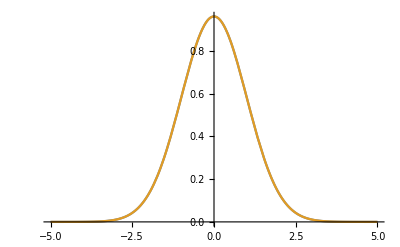

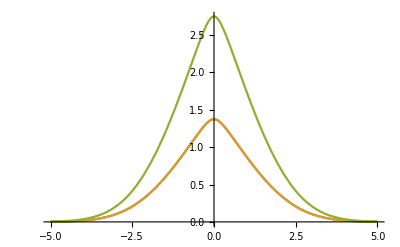

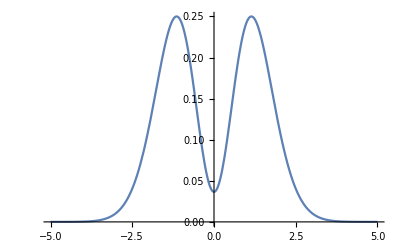

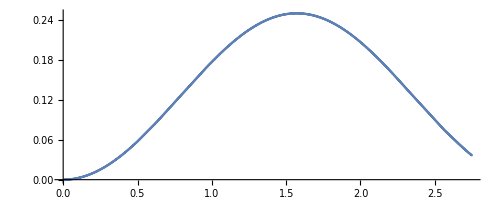

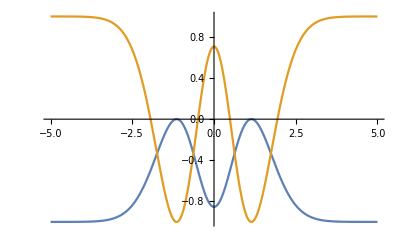

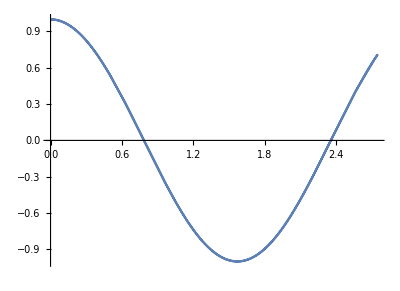

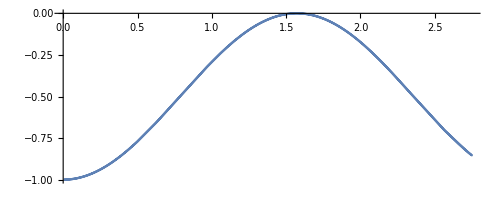

```mathematica
Clear[as,c]
BmapFull[a_,b_,p_,T_,c_]:=1/Sqrt[2]*If[c==1,a*Sqrt[T]+I*Exp[I*p]*b*Sqrt[1-T],b*Sqrt[T]+I*Exp[-I*p]*a*Sqrt[1-T]]
cf1=Coefficient[BmapFull[as,b,ϕ,Sin[α]^2,1]*BmapFull[c,d,ϕ,Sin[β]^2,1]+BmapFull[as,b,ϕ,Sin[α]^2,0]*BmapFull[c,d,ϕ,Sin[β]^2,0],b*c];
cf2=Coefficient[BmapFull[as,b,ϕ,Sin[α]^2,1]*BmapFull[c,d,ϕ,Sin[β]^2,1]+BmapFull[as,b,ϕ,Sin[α]^2,0]*BmapFull[c,d,ϕ,Sin[β]^2,0],b*d];
cf3=Coefficient[BmapFull[as,b,ϕ,Sin[α]^2,1]*BmapFull[c,d,ϕ,Sin[β]^2,1]+BmapFull[as,b,ϕ,Sin[α]^2,0]*BmapFull[c,d,ϕ,Sin[β]^2,0],as*c];
cf4=Coefficient[BmapFull[as,b,ϕ,Sin[α]^2,1]*BmapFull[c,d,ϕ,Sin[β]^2,1]+BmapFull[as,b,ϕ,Sin[α]^2,0]*BmapFull[c,d,ϕ,Sin[β]^2,0],as*d];
FullSimplify[Refine[FullSimplify[(cf3*Conjugate[cf3])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]]

Ecorr[α_,β_]:=-(Sin[α+β]^2-Cos[α+β]^2)
S[α_,β_,αp_,βp_]:=Ecorr[α,β]-Ecorr[α,βp]+Ecorr[αp,βp]+Ecorr[αp,β]
Corr[α_,β_]:=1/4 Sin[α+β]^2
TransferDist[z_,z0_,A_]:=A*Exp[-(z-z0)^2/2];
PhaseDist[z_,z0_,A_]:=ArcSin[Sqrt[TransferDist[z,z0,A]]]
a=0
A=0.96194;(*0.5;*)(*0.691342*)

Plot[{TransferDist[x,a,A],TransferDist[x,-a,A]},{x,-5,5}]
Plot[{PhaseDist[x,a,A],PhaseDist[x,-a,A],PhaseDist[x,a,A]+PhaseDist[x,-a,A]},{x,-5,5}]
Plot[{Corr[PhaseDist[x,a,A],PhaseDist[x,-a,A]]},{x,-5,5}]
ParametricPlot[{PhaseDist[x,a,A]+PhaseDist[x,-a,A],Corr[PhaseDist[x,a,A],PhaseDist[x,-a,A]]},{x,-5,5}]
Plot[{(TransferDist[x,a,A])*(1-TransferDist[x,-a,A])+(1-TransferDist[x,a,A])*(TransferDist[x,-a,A])-(1-TransferDist[x,a,A])*(1-TransferDist[x,-a,A])-(TransferDist[x,a,A])*(TransferDist[x,-a,A]),Ecorr[PhaseDist[x,a,A],PhaseDist[x,-a,A]]},{x,-5,5}]
ParametricPlot[{PhaseDist[x,a,A]+PhaseDist[x,-a,A],Ecorr[PhaseDist[x,a,A],PhaseDist[x,-a,A]]},{x,-5,5}]
ParametricPlot[{PhaseDist[x,a,A]+PhaseDist[x,-a,A],(TransferDist[x,a,A])*(1-TransferDist[x,-a,A])+(1-TransferDist[x,a,A])*(TransferDist[x,-a,A])-(1-TransferDist[x,a,A])*(1-TransferDist[x,-a,A])-(TransferDist[x,a,A])*(TransferDist[x,-a,A])},{x,-5,5}]
```

```mathematica
N[Sin[Pi/2]]
```

1.

```mathematica
N[S[5/16*Pi,Pi*8/16,8/16*Pi,Pi*5/16]]
```

-2.47247

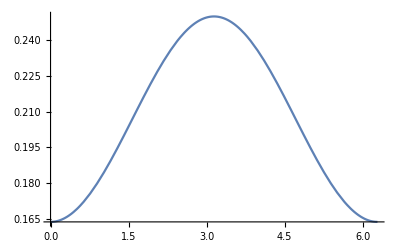

```mathematica
Plot[1/4 ⅇ^(-ⅈ ϕ) (ⅇ^(ⅈ Conjugate[ϕ]) Cos[2/5*Pi] Cos[2/5*Pi]-Sin[2/5*Pi] Sin[2/5*Pi]) (Cos[2/5*Pi] Cos[2/5*Pi]-ⅇ^(ⅈ ϕ) Sin[2/5*Pi] Sin[2/5*Pi]),{ϕ,0,2*Pi}]
```

```mathematica
FullSimplify[(Refine[FullSimplify[(cf3*Conjugate[cf3])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]+Refine[FullSimplify[(cf2*Conjugate[cf2])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]-Refine[FullSimplify[(cf1*Conjugate[cf1])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]-Refine[FullSimplify[(cf4*Conjugate[cf4])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}])/(Refine[FullSimplify[(cf3*Conjugate[cf3])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]+Refine[FullSimplify[(cf2*Conjugate[cf2])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]+Refine[FullSimplify[(cf1*Conjugate[cf1])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}]+Refine[FullSimplify[(cf4*Conjugate[cf4])],{α>0,α<Pi/2,β>0,β<Pi/2,ϕ>0,ϕ1>0,ϕ2>0}])]
```

Cos[2 α] Cos[2 β]-Cos[2 ϕ] Sin[2 α] Sin[2 β]

```mathematica
α0 = Pi*4/5;
Manipulate[Plot[{Cos[2 α0] Cos[2 α0]-Cos[2 ϕ] Sin[2 α0] Sin[2 α0],Cos[2 α0] Cos[2 α0]-4 Cos[α0] Cos[α0] Cos[ϕ] Sin[α0] Sin[α0]},{ϕ,0,2*Pi}],{ α0,0,Pi}]
```

```mathematica
Manipulate[Plot[{Cos[2 α0] Cos[2 α0]-Cos[2 ϕ] Sin[2 α0] Sin[2 α0],Cos[2 α0] Cos[2 α0]-4 Cos[α0] Cos[α0] Cos[ϕ] Sin[α0] Sin[α0]},{ α0,0,Pi/2*1.1}], {ϕ,0,2*Pi}]
```

```mathematica
Maximize[{x+2 y,x^2+2 y^2≤3&&x+y==2&&x≥1},{x,y}]
```

```mathematica
Maximize[{x-2 y,x^2+y^2≤1},{x,y}]
```

{√5,{x→1/(√5),y→-2/(√5)}}

```mathematica
FindMaximum[{S[x1,y1,x2,y2]},{x1,y1,x2,y2}]
```

{2.82843,{x1→0.981748,y1→1.76715,x2→1.76715,y2→0.981748}}

```mathematica
N[{0.9817477042468129,1.7671458676442613,1.7671458676442613,0.9817477042468129}/Pi*16]
```

{5.,9.,9.,5.}

```mathematica
N[Sin[5*Pi/16]^2]
```

0.691342

```mathematica
FindMaximum[{S[Pi/2,y1,x2,y2]},{y1,x2,y2}]
```

{2.82843,{y1→1.1781,x2→2.35619,y2→0.392699}}